```mathematica
root = "/home/boxx/bees";
datadir = FileNameJoin[{root, "images4nets/subgenera"}];
bifariousdir=FileNameJoin[{datadir, "Separatobombus_just_cropped"}];
melanopygusdir = FileNameJoin[{datadir, "Thoracobombus_just_cropped"}];
culludir = FileNameJoin[{datadir, "Cullumanobombus_just_cropped"}];
bifariousdir1=FileNameJoin[{datadir, "Separatobombus_rotate"}];
melanopygusdir1 = FileNameJoin[{datadir, "Thoracobombus_rotate"}];
culludir1 = FileNameJoin[{datadir, "Cullumanobombus_rotate"}];
bifariousdir2=FileNameJoin[{datadir, "Separatobombus_flip"}];
melanopygusdir2 = FileNameJoin[{datadir, "Thoracobombus_flip"}];
culludir2 = FileNameJoin[{datadir, "Cullumanobombus_flip"}];
bifarfiles=FileNames["*.jpg", bifariousdir];
melanofiles = FileNames["*.jpg", melanopygusdir];
cullufiles = FileNames["*.jpg", culludir];
bifarfiles1=FileNames["*.jpg", bifariousdir1];
melanofiles1 = FileNames["*.jpg", melanopygusdir1];
cullufiles1 = FileNames["*.jpg", culludir1];
bifarfiles2=FileNames["*.jpg", bifariousdir2];
melanofiles2 = FileNames["*.jpg", melanopygusdir2];
cullufiles2 = FileNames["*.jpg", culludir2];
{Length@bifarfiles1, Length@melanofiles1, Length@cullufiles1}
```

{1264,1346,1842}

```mathematica
Needs["CUDALink`"]
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx10g"];
```

```mathematica
bifardat=ParallelMap[Import[#]&,bifarfiles];
melanodat=ParallelMap[Import[#]&,melanofiles];
culludat=ParallelMap[Import[#]&,cullufiles];
bifardat1=ParallelMap[Import[#]&,bifarfiles1];
melanodat1=ParallelMap[Import[#]&,melanofiles1];
culludat1=ParallelMap[Import[#]&,cullufiles1];
bifardat2=ParallelMap[Import[#]&,bifarfiles2];
melanodat2=ParallelMap[Import[#]&,melanofiles2];
culludat2=ParallelMap[Import[#]&,cullufiles2];
```

```mathematica
{Dimensions@bifardat, Dimensions@melanodat, Dimensions@culludat}
```

{{632},{673},{921}}

```mathematica
RandomSample[bifardat, 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[melanodat,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dat=RandomSample@Join[Thread[bifardat->"separato"],Thread[melanodat->"thoraco"], Thread[culludat->"cullu"],Thread[bifardat1->"separato"],Thread[melanodat1->"thoraco"], Thread[culludat1->"cullu"], Thread[bifardat2->"separato"],Thread[melanodat2->"thoraco"],  Thread[culludat2->"cullu"]];
Dimensions@dat
```

{13356}

```mathematica
RandomSample[dat,10]
```

{-Graphics-→thoraco,-Graphics-→cullu,-Graphics-→thoraco,-Graphics-→separato,-Graphics-→thoraco,-Graphics-→separato,-Graphics-→cullu,-Graphics-→thoraco,-Graphics-→thoraco,-Graphics-→cullu}

```mathematica
bifEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,bifardat];
melEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,melanodat];
culEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,culludat];
```

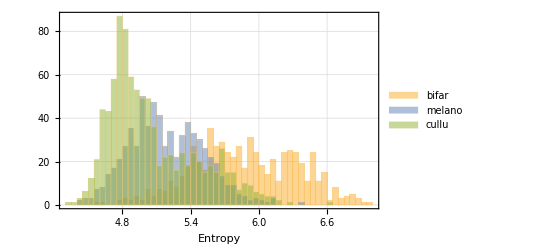

```mathematica
Histogram[{bifEntropy,melEntropy, culEntropy},40,ChartLegends->{"bifar","melano", "cullu"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

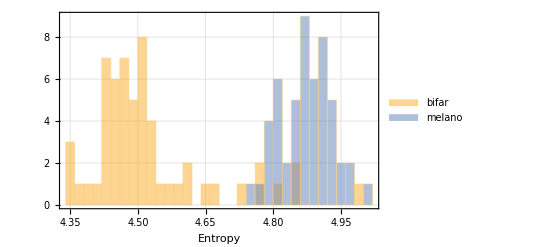

```mathematica
Histogram[{Map[Mean,Partition[bifEntropy,108]],Map[Mean,Partition[melEntropy,108]]},40,ChartLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

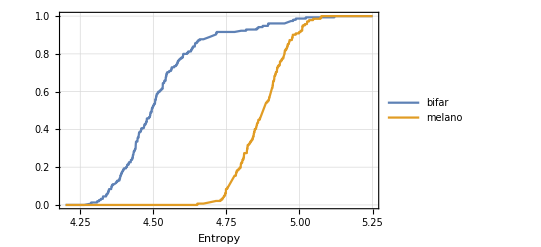

```mathematica
Plot[{CDF[EmpiricalDistribution[Map[Mean, Partition[bifEntropy,40]]],x], CDF[EmpiricalDistribution[Map[Mean, Partition[melEntropy, 40]]],x]},{x,4.2,5.25},PlotLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

```mathematica
rs=RandomSample[Range[Length[dat]]];
tix=rs[[1;;Round[Length[dat]*0.7]]];
vix=rs[[Round[Length[dat]*0.7]+1;;Round[Length[dat]*0.9]]];
ttix=rs[[Round[Length[dat]*0.9]+1;;]];
{Length@tix,Length@vix,Length@ttix}
```

{9349,2671,1336}

```mathematica
networkdir=FileNameJoin[{root,"networks"}];
net=NetChain[
{
ConvolutionLayer[50,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{3,3},{2,2}],
ConvolutionLayer[100,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DropoutLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DropoutLayer[],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"separato","thoraco", "cullu"}}],
"Input"->NetEncoder[{"Image",{220,298}}]
]
```

NetChain[<>]

```mathematica
net=NetTrain[net,dat[[tix]],ValidationSet->dat[[vix]],TargetDevice->"GPU","Method"->{"ADAM","L2Regularization"->1,"InitialLearningRate"->0.00001}, MaxTrainingRounds->20];
```

```mathematica
.
```

```mathematica
%61
```

NetChain[<>]

```mathematica
cm=ClassifierMeasurements[net,dat[[ttix]]];
```

Part::pkspec1: The expression ttix cannot be used as a part specification.

ClassifierMeasurements::wrgfunc: The first argument should be a ClassifierFunction instead of net.

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.818114

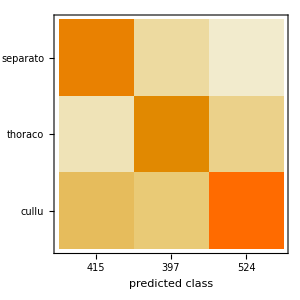

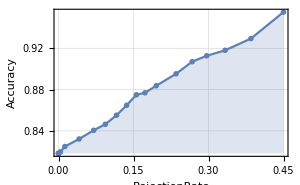

{-Graphics-→thoraco,-Graphics-→cullu,-Graphics-→thoraco,-Graphics-→thoraco,-Graphics-→separato,-Graphics-→cullu,-Graphics-→cullu,-Graphics-→thoraco,-Graphics-→cullu,-Graphics-→cullu}

```mathematica
cm["ConfusionMatrixPlot"]
cm["AccuracyRejectionPlot"]
cm["WorstClassifiedExamples"]
```

```mathematica
Decode = NetDecoder["Image"]
Decode[NetExtract[net, {1, "Weights"}]]
```

NetDecoder[<>]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
testDatBifar=Select[dat[[ttix]],Values@#=="bifar"&];
testDatMelano=Select[dat[[ttix]],Values@#=="melano"&];
```

```mathematica
pTestDatBifar=net[Keys@testDatBifar,{"Probability","bifar"}];
pTestDatMelano=net[Keys@testDatMelano,{"Probability","bifar"}];
```

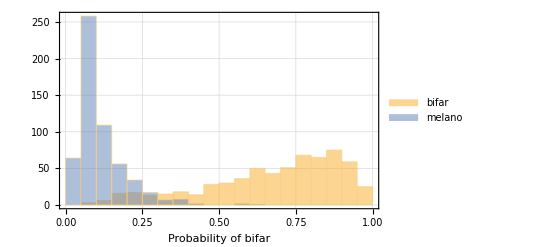

```mathematica
Histogram[{pTestDatBifar,pTestDatMelano},20,GridLines->Automatic,GridLinesStyle->Directive[Dotted,Gray],Frame->True,FrameLabel->{"Probability of bifar"},ChartLegends->{"bifar","melano"}]
```

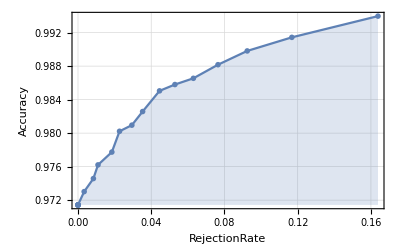

```mathematica
Show[
cm["AccuracyRejectionPlot"],
GridLines->Automatic,
GridLinesStyle->Directive[Dotted, Gray]
]
```